## Prep

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/Documents/gr1d/GR1D_HIPACC2014

```mathematica
imgSize=800;
```

## Process

```mathematica
data=Import["Data/rho_c_t.dat"]
```

{{0.,9.72648×10^9},{0.000101979,9.70358×10^9},{0.00020346,9.68058×10^9},{0.000306001,9.65815×10^9},{0.0004085,9.63653×10^9},3113,{0.20157,3.68637×10^14},{0.20167,3.68637×10^14},{0.20177,3.68637×10^14},{0.20187,3.68637×10^14}}
 |  |  |  |

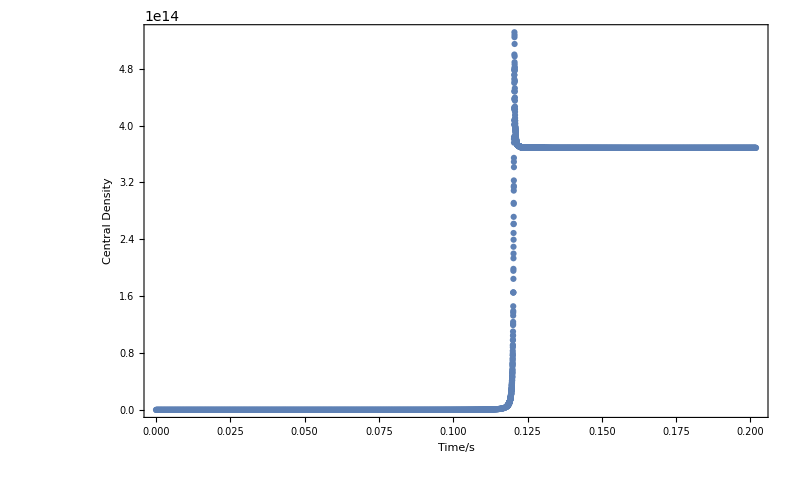

cdVSt.png

```mathematica
lstplt=ListPlot[data,Frame->True,ImageSize->imgSize,FrameLabel->{"Time/s","Central Density"}]
Export["cdVSt.png",lstplt]
```

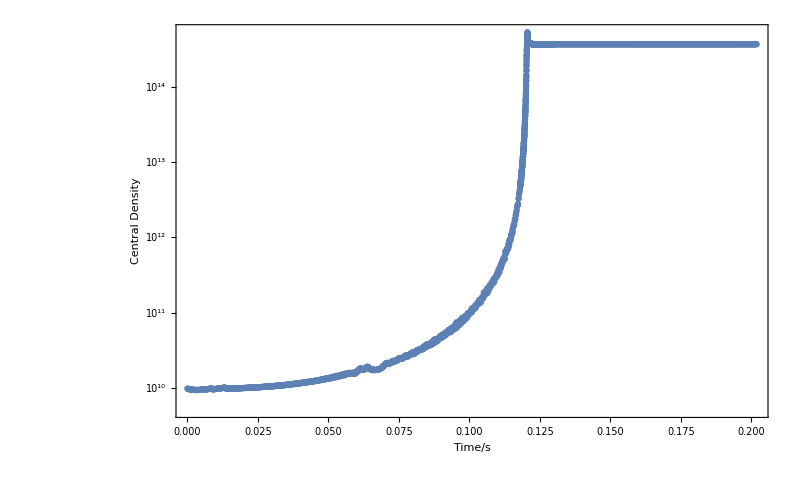

cdVStlog.png

```mathematica
ListLogPlot[data,Frame->True,ImageSize->imgSize,FrameLabel->{"Time/s","Central Density"}]
Export["cdVStlog.png",%]
```